```mathematica
A DsixTools Program
This notebook shows how to introduce SMEFT input values in DsixTools directly.
```

## Start DsixTools

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../../"];
Needs["DsixTools`"]
```

## Generate input values

## Options

```mathematica
Init[gs] = Sqrt[4Pi (0.107809)];
NewScale["low", 173.21];
NewScale["high", 10^4];

10^tLOW
```

173.21

```mathematica
CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;
```

## SM parameters

```mathematica
Init[g]=e/Sin[θW];
Init[gp]=e/Cos[θW];

gstrong = Sqrt[4Pi (0.107809)];
```

```mathematica
Init[λ]=mh^2/v^2;
Init[m2]=mh^2/2;
```

```mathematica
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
```

```mathematica
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
```

```mathematica
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
```

```mathematica
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

## Load SMEFTrunner module

```mathematica
LoadModule["SMEFTrunner"]
```

LoadModule::Already: Warning : SMEFTrunner module already loaded

## Use SMEFTrunner module

```mathematica
LoadBetaFunctions;
```

Loading SMEFT β functions

```mathematica
RunRGEsSMEFT;
```

Running

Running finished!

## Results after SMEFTrunner

```mathematica
(* We find the position of Subscript[(Subscript[C, ll]), 1112] in Parameters *)
FindParameterSMEFT[gs]
```

{3}

```mathematica
outSMEFTrunner[[3]]/.t->tHIGH
outSMEFTrunner[[3]]/.t->tLOW
gstrong
```

0.983713

1.21823

1.16394

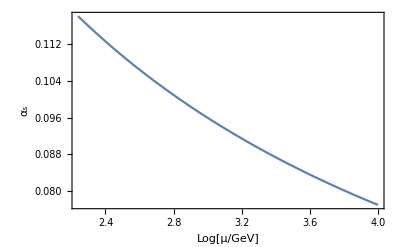

```mathematica
(* Wilson coefficients *)
plotWC=Plot[outSMEFTrunner[[3]]^2/(4π),{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[μ/GeV]","α_s",None,None}]
```

```mathematica
(* Finally, one can also export the results to a file *)
```

```mathematica
ExportSMEFTrunner;
```

```mathematica
10^tLOW
LOWSCALE
```

173.21

173.21

```mathematica
tLOW
```

2.23857

```mathematica
tHIGH
```

4